```mathematica
Export["/home/unkokusei/MyDocuments/work/thesis/figures/ripple/ang_abs_factor.dat", Table[{i,i^2}, {i, 10}]]
```

/home/unkokusei/MyDocuments/work/thesis/figures/ripple/out.dat

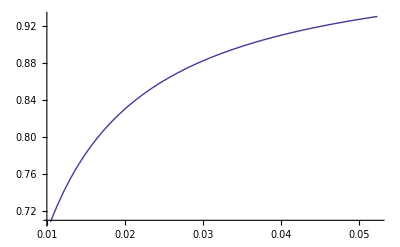

```mathematica
g[ω_,θ_]:=1/Sin[ω]+1/Sin[2θ-ω]
A[ω_,θ_]:=μ/t(1-Exp[-t/μ g[ω,θ]])/g[ω,θ]

th[qz_]:=λ qz/(4π)
w=0.6*π/180;(*rad*)
λ=1.175;(*Angstrom*)
μ=2600;(*um*)
t=10;(*um*)
Plot[A[θ,θ],{θ,0.6Degree,3Degree}]
```

```mathematica
Export["/home/unkokusei/MyDocuments/work/thesis/figures/ripple/abs_factor.dat", Table[{i,i^2}, {i, 10}]]
```

```mathematica
Table[i,{i,0,2,0.2}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

```mathematica
0.5 Degree
```

0.00872665